```mathematica
Needs["NumericalCalculus`"];
Needs["ColorBar`"];
```

## Precompute joint element

```mathematica
precomputeElement[EJ1_,EJ2_]:=Module[{t1,ϕ,ϕ1,int1,res},
t1=Monitor[Table[
res=Table[
FindMinimum[-EJ1 Cos[ϕ1]-EJ2 Cos[ϕ-ϕ1], {ϕ1, s1}][[1]]
,{s1,-π,π,π/3.}];
{ϕ, Min[res]}
,{ϕ,-2π,2.π,π/1000.}],ϕ];
Return[Interpolation[t1]];
(*Return[t1];*)
];

getEnergy[int1_, ϕ_]:=Module[{},
Return[int1[Mod[ϕ+2π,4π]-2π]];
];
getEnergyJJ[EJ_, ϕ_]:=Module[{},
Return[-EJ*Cos[ϕ]];
];
getEnergyLinInd[EL_, ϕ_]:=Module[{},
Return[EL/2 ϕ^2];
];
```

## Set up

In the unit of GHz

```mathematica
sf=10^-9/(2 π 1*10^-34);
Ic1=Quantity[5*10^-6,"Ampere"];
EJ1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic1 1/Quantity["Joule"],"SI"]
(*EJ2=α EJ1*)
(*EL=β EJ1*)
Subscript[H, arm][α_]:=Quiet[precomputeElement[EJ1,α EJ1]];
```

2618.942

## Hamiltonian on the arms

```mathematica
αlist=Table[i,{i,1,1}]
αlistname=Table["α="<>(ToString[αlist[[i]]]),{i,1,Length[αlist]}];
```

{1}

```mathematica
Subscript[listH, arm]=Monitor[Table[Subscript[H, arm][αlist[[i]]],{i,1,Length[αlist]}],αlist[[i]]];
```

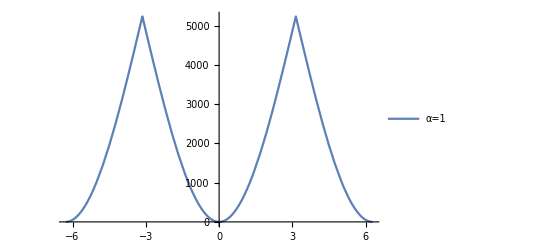

```mathematica
Subscript[xH, arm]=Table[getEnergy[Subscript[listH, arm][[i]],x]-getEnergy[Subscript[listH, arm][[i]],0],{i,1,Length[αlist]}];
Plot[Evaluate[Subscript[xH, arm]],{x,-2π,2π},PlotLegends->αlistname]
```

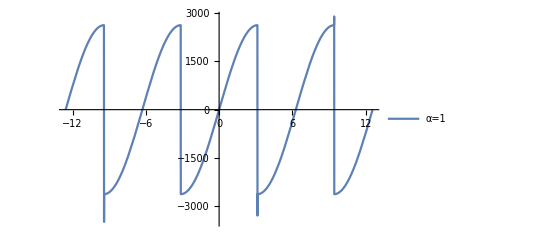

```mathematica
Plot[Evaluate[Table[D[Subscript[xH, arm][[i]],x]/.x->y,{i,1,Length[Subscript[listH, arm]]}]],{y,-4π,4π},PlotLegends->αlistname]
```

## Total Hamiltonian

```mathematica
H[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕext_,Harm_,β_]:=
(getEnergy[Harm,ϕ1-ϕ2-ϕext/4]+getEnergy[Harm,ϕ2-ϕ3-ϕext/4]+ getEnergy[Harm,ϕ3-ϕ4-ϕext/4]+getEnergy[Harm,ϕ4-ϕ1-ϕext/4]-4getEnergy[Harm,0])+(getEnergyLinInd[β EJ1,ϕ1-ϕ5]+getEnergyLinInd[β EJ1,ϕ2-ϕ5]+getEnergyLinInd[β EJ1,ϕ3-ϕ5]+getEnergyLinInd[β EJ1,ϕ4-ϕ5]);
Hn[ϕ1_?NumericQ,ϕ2_?NumericQ,ϕ3_?NumericQ,ϕ4_?NumericQ,ϕ5_?NumericQ,ϕext_?NumericQ,Harm_,β_?NumericQ]:=(getEnergy[Harm,ϕ1-ϕ2-ϕext/4]+getEnergy[Harm,ϕ2-ϕ3-ϕext/4]+ getEnergy[Harm,ϕ3-ϕ4-ϕext/4]+getEnergy[Harm,ϕ4-ϕ1-ϕext/4]-4getEnergy[Harm,0])+(getEnergyLinInd[β EJ1,ϕ1-ϕ5]+getEnergyLinInd[β EJ1,ϕ2-ϕ5]+getEnergyLinInd[β EJ1,ϕ3-ϕ5]+getEnergyLinInd[β EJ1,ϕ4-ϕ5]);
```

### Fix β, Varying α

```mathematica
β=2.5;
ip=Table[RandomReal[{0,2π},4],100];
```

```mathematica
Monitor[For[listt1={};j=1,j<=Length[αlist],j++,
Monitor[
t1=Table[
zt=Sort[Table[
res=Quiet[FindMinimum[Hn[ϕ1,ϕ2,ϕ3,ϕ4,0,ϕext,Subscript[listH, arm][[j]],β],{ϕ1,ip[[i,1]]},{ϕ2,ip[[i,2]]},{ϕ3,ip[[i,3]]},{ϕ4,ip[[i,4]]}]];
{res[[1]],ϕ1,ϕ2,ϕ3,ϕ4}/.res[[2]]
,{i,Length[ip]}]];
zt1={Flatten[{ϕext, zt[[1]]}]}
,{ϕext,-4π,4π,π/20}]
,ϕext];
listt1=Insert[listt1,t1,j]
],
αlist[[j]]]
```

```mathematica
Export["listt1.txt",listt1];
```

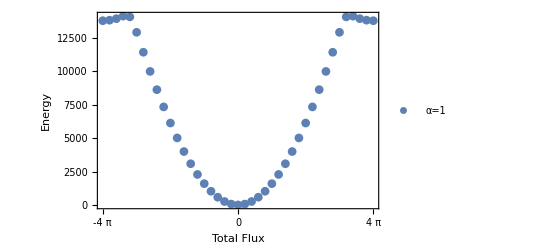

```mathematica
ListPlot[
Table[listt1[[i,All,1,{1,2}]],{i,1,Length[listt1]}],
 PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Energy"}, FrameTicks->{Automatic,{π Range[-8,8],None}},PlotLegends->αlistname
]
```

Find Derivatives

```mathematica
Monitor[
For[listt2={};j=1,j<=Length[αlist],j++,
Monitor[
t2=Table[
{ϕext,ϕ1,ϕ2,ϕ3,ϕ4}=listt1[[j,i,1,{1,3,4,5,6}]];
ϕf=0;

h0=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕ1,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕ2,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕ3,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕ4,-a ϕw+ϕf, ϕext,Subscript[listH, arm][[j]],β];
{ϕext,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,2},0])/2,
(*(ND[ND[ND[h0/.{a->1,ϕw->0},{ϕx,1},0],{ϕy,1},0],{ϕz,1},0]),*)
xyzvalue,
(ND[ND[h0/.{a->1,ϕz->0,ϕw->0},{ϕx,2},0],{ϕy,2},0])/4,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,4},0])/24
}
,{i,Length[listt1[[j]]]}]
,listt1[[j,i,1,1]]];
listt2=Insert[listt2,t2,j]]
,αlist[[j]]]
```

```mathematica
Export["listt2.txt",listt2];
```

```mathematica
x2α=Table[Interpolation[listt2[[i,All,{1,2}]]],{i,1,Length[αlist]}];
(*xyzα=Table[Interpolation[listt2[[i,All,{1,3}]]],{i,1,Length[αlist]}];*)
x2y2α=Table[Interpolation[listt2[[i,All,{1,4}]]],{i,1,Length[αlist]}];x4α=Table[Interpolation[listt2[[i,All,{1,5}]]],{i,1,Length[αlist]}];
```

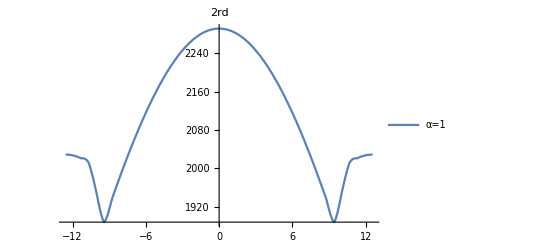

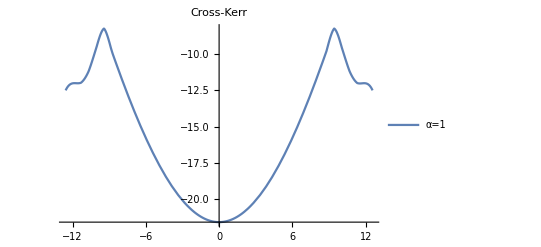

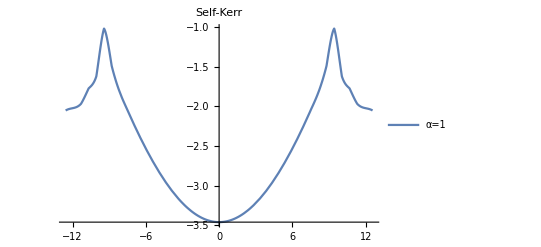

```mathematica
Plot[Evaluate[Table[x2α[[i]][x],{i,1,Length[αlist]}]],{x,-4π,4π},PlotLabel->"2rd",PlotLegends->αlistname,PlotRange->All]

(*Plot[Evaluate[Table[xyzα[[i]][x],{i,1,Length[αlist]}]],{x,-4π,4π},PlotLabel->"3rd",PlotLegends->αlistname,PlotRange->All]*)
Plot[Evaluate[Table[x2y2α[[i]][x],{i,1,Length[αlist]}]],{x,-4π,4π},PlotLabel->"Cross-Kerr",PlotLegends->αlistname,PlotRange->All]
Plot[Evaluate[Table[x4α[[i]][x],{i,1,Length[αlist]}]],{x,-4π,4π},PlotLabel->"Self-Kerr",PlotLegends->αlistname,PlotRange->All]

(*Plot[{Evaluate[Table[x2α[[i]][x],{i,1,Length[αlist]}]],Evaluate[Table[xyzα[[i]][x],{i,1,Length[αlist]}]],Evaluate[Table[x4α[[i]][x],{i,1,Length[αlist]}]],Evaluate[Table[x2y2α[[i]][x],{i,1,Length[αlist]}]]},{x,-4π,4π},PlotLegends->{"2nd x^2","3rd","self_kerr","cross_kerr x^2y^2"},PlotRange->All]*)
```

### Phase Diagram α

```mathematica
lenϕ=Length[Table[i,{i,-4Pi,4Pi,Pi/5}]];
lenα=Length[αlist];
```

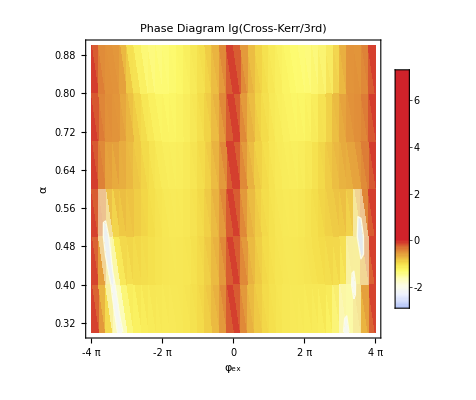

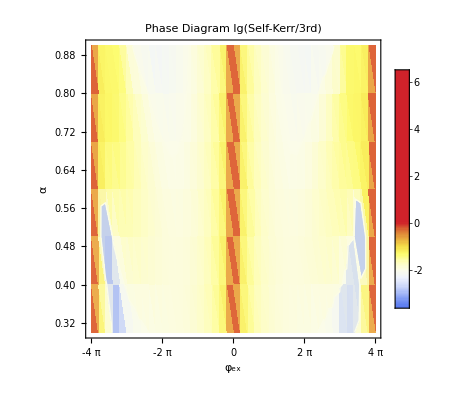

```mathematica
tableαcrossvs3rd=Flatten[Table[{listt2[[j,i,1]],αlist[[j]],Log10[Abs[listt2[[j,i,4]]/listt2[[j,i,3]]]]},{i,1,lenϕ},{j,1,lenα}],1];
tableαselfvs3rd=Flatten[Table[{listt2[[j,i,1]],αlist[[j]],Log10[Abs[listt2[[j,i,5]]/listt2[[j,i,3]]]]},{i,1,lenϕ},{j,1,lenα}],1];

ListDensityPlot[
tableαcrossvs3rd,
PlotLegends->Automatic,FrameLabel->{"φ_ex","α"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{1/2π Range[-8,8],None}},FrameTicksStyle->Directive[6],PlotLabel->Style["Phase Diagram lg(Cross-Kerr/3rd)",14],PlotRange->All,Mesh->1,MeshStyle->Black,MeshFunctions->{Boole[Greater[#3,-2]]&},ColorFunction->(ColorData[{"TemperatureMap",{-4,0}}]),ColorFunctionScaling->False
]

ListDensityPlot[
tableαselfvs3rd,
PlotLegends->Automatic,FrameLabel->{"φ_ex","α"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{1/2π Range[-8,8],None}},FrameTicksStyle->Directive[6],PlotLabel->Style["Phase Diagram lg(Self-Kerr/3rd)",14],PlotRange->All,Mesh->1,MeshStyle->Black,MeshFunctions->{Boole[Greater[#3,-2]]&},ColorFunction->(ColorData[{"TemperatureMap",{-4,0}}]),ColorFunctionScaling->False
]
```

### Fix α, Varying β

```mathematica
α=0.5;
Subscript[hereH, arm]=Subscript[listH, arm][[3]];
βlist=Table[0.2i+1,{i,0,10}]
βlistname=Table["β="<>(ToString[βlist[[i]]]),{i,1,Length[βlist]}];
ip=Table[RandomReal[{0,2π},4],20];
```

{1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.}

```mathematica
Monitor[For[listt3={};j=1,j<=Length[βlist],j++,
Monitor[
t3=Table[
zt=Sort[Table[
res=Quiet[FindMinimum[Hn[ϕ1,ϕ2,ϕ3,ϕ4,0,ϕext,Subscript[hereH, arm],βlist[[j]]],{ϕ1,ip[[i,1]]},{ϕ2,ip[[i,2]]},{ϕ3,ip[[i,3]]},{ϕ4,ip[[i,4]]}]];
{res[[1]],ϕ1,ϕ2,ϕ3,ϕ4}/.res[[2]]
,{i,Length[ip]}]];
zt1={Flatten[{ϕext, zt[[1]]}]}
,{ϕext,-4π,4π,π/5}]
,ϕext];
listt3=Insert[listt3,t3,j]
],
βlist[[j]]]
```

```mathematica
Export["listt3.txt",listt3];
```

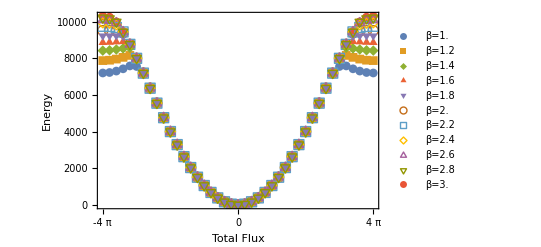

```mathematica
ListPlot[
Table[listt3[[i,All,1,{1,2}]],{i,1,Length[listt3]}],
 PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Energy"}, FrameTicks->{Automatic,{π Range[-8,8],None}},PlotLegends->βlistname
]
```

Find Derivatives

```mathematica
Monitor[
For[listt4={};j=1,j<=Length[βlist],j++,
Monitor[
t4=Table[
{ϕext,ϕ1,ϕ2,ϕ3,ϕ4}=listt3[[j,i,1,{1,3,4,5,6}]];
ϕf=0;

h0=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕ1,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕ2,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕ3,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕ4,-a ϕw+ϕf, ϕext,Subscript[hereH, arm],βlist[[j]]];
{ϕext,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,2},0])/2,
(ND[ND[ND[h0/.{a->1,ϕw->0},{ϕx,1},0],{ϕy,1},0],{ϕz,1},0]),
(*xyzvalue,*)
(ND[ND[h0/.{a->1,ϕz->0,ϕw->0},{ϕx,2},0],{ϕy,2},0])/4,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,4},0])/24
}
,{i,Length[listt3[[j]]]}]
,listt3[[j,i,1,1]]];
listt4=Insert[listt4,t4,j]]
,βlist[[j]]]
```

```mathematica
Export["listt4.txt",listt4];
```

```mathematica
x2β=Table[Interpolation[listt4[[i,All,{1,2}]]],{i,1,Length[βlist]}];
xyzβ=Table[Interpolation[listt4[[i,All,{1,3}]]],{i,1,Length[βlist]}];x2y2β=Table[Interpolation[listt4[[i,All,{1,4}]]],{i,1,Length[βlist]}];x4β=Table[Interpolation[listt4[[i,All,{1,5}]]],{i,1,Length[βlist]}];
```

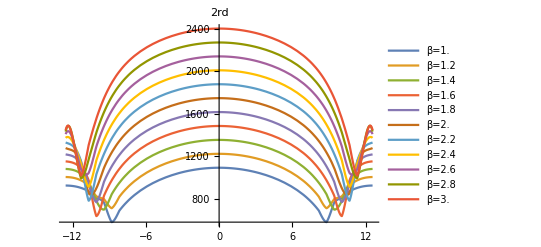

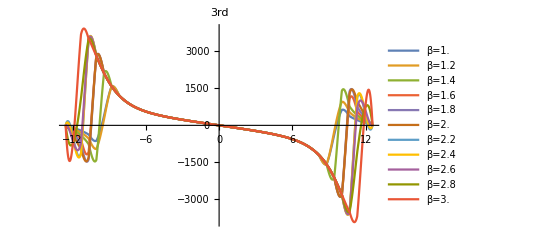

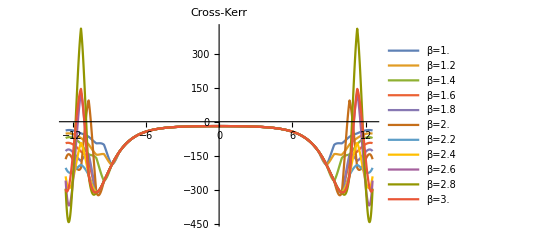

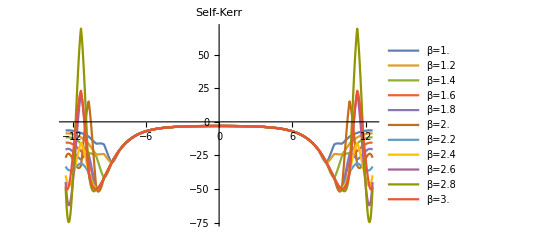

```mathematica
Plot[Evaluate[Table[x2β[[i]][x],{i,1,Length[βlist]}]],{x,-4π,4π},PlotLabel->"2rd",PlotLegends->βlistname,PlotRange->All]
Plot[Evaluate[Table[xyzβ[[i]][x],{i,1,Length[βlist]}]],{x,-4π,4π},PlotLabel->"3rd",PlotLegends->βlistname,PlotRange->All]
Plot[Evaluate[Table[x2y2β[[i]][x],{i,1,Length[βlist]}]],{x,-4π,4π},PlotLabel->"Cross-Kerr",PlotLegends->βlistname,PlotRange->All]
Plot[Evaluate[Table[x4β[[i]][x],{i,1,Length[βlist]}]],{x,-4π,4π},PlotLabel->"Self-Kerr",PlotLegends->βlistname,PlotRange->All]
```

### Phase Diagram β

```mathematica
lenϕ=Length[Table[i,{i,-4Pi,4Pi,Pi/5}]];
lenβ=Length[βlist];
```

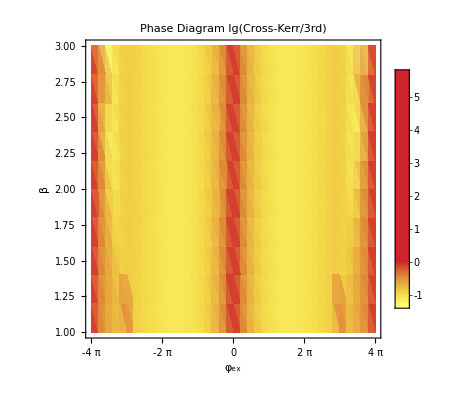

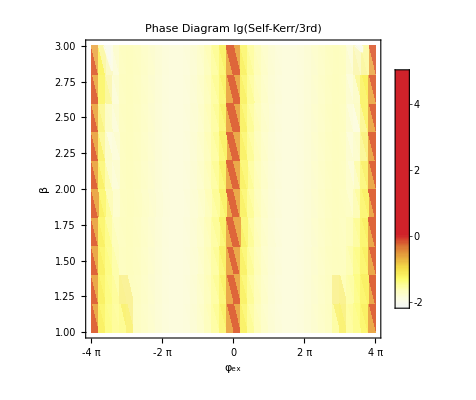

```mathematica
tableβcrossvs3rd=Flatten[Table[{listt4[[j,i,1]],βlist[[j]],Log10[Abs[listt4[[j,i,4]]/listt4[[j,i,3]]]]},{i,1,lenϕ},{j,1,lenβ}],1];
tableβselfvs3rd=Flatten[Table[{listt4[[j,i,1]],βlist[[j]],Log10[Abs[listt4[[j,i,5]]/listt4[[j,i,3]]]]},{i,1,lenϕ},{j,1,lenβ}],1];


ListDensityPlot[
tableβcrossvs3rd,
PlotLegends->Automatic,FrameLabel->{"φ_ex","β"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[-4,4],π Range[-4,4]}},PlotLabel->Style["Phase Diagram lg(Cross-Kerr/3rd)",14],PlotRange->All,Mesh->3,MeshStyle->Black,MeshFunctions->{Boole[Greater[#3,-2]]&},ColorFunction->(ColorData[{"TemperatureMap",{-4,0}}]),ColorFunctionScaling->False
]
ListDensityPlot[
tableβselfvs3rd,
PlotLegends->Automatic,FrameLabel->{"φ_ex","β"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[-4,4],None}},PlotLabel->Style["Phase Diagram lg(Self-Kerr/3rd)",14],PlotRange->All,Mesh->1,MeshStyle->Black,MeshFunctions->{Boole[Greater[#3,-2]]&},ColorFunction->(ColorData[{"TemperatureMap",{-4,0}}]),ColorFunctionScaling->False
]
```

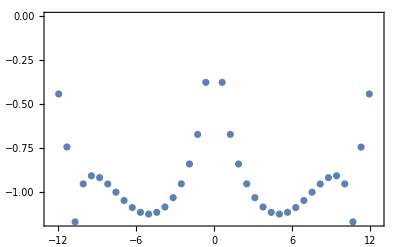

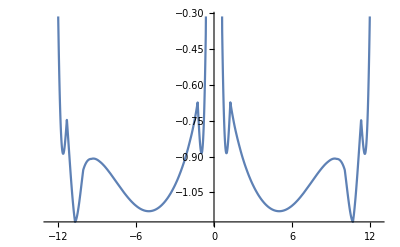

```mathematica
ttt=Table[{listt4[[9,i,1]],Log10[Abs[listt4[[9,i,4]]/listt4[[9,i,3]]]]},{i,1,lenϕ}];
ittt=Interpolation[ttt];
ListPlot[ttt,Frame->True,FrameTicks->All]
Plot[ittt[x],{x,-4Pi,4Pi}]
```